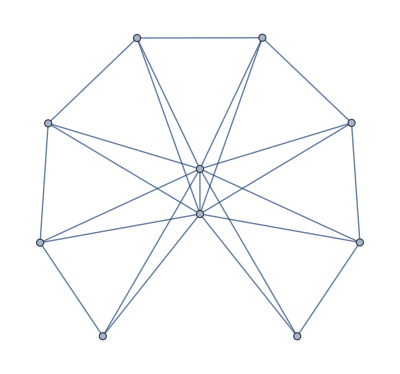

```mathematica
g=Graph[Flatten[Join[{1<->2,2<->3,1<->3},Table[{i<->1,i<->i-1,i<->2},{i,4,10}]]]]
```

```mathematica
MaximalPlanarQ[g]
```

True

```mathematica
MinimalSolGraph[max_]:=Graph[Flatten[Join[{1<->2,2<->3,1<->3},Table[{i<->1,i<->i-1,i<->2},{i,4,max}]]]]
```

```mathematica
SummarizeFormula[list_]:=Sort[Tally[Map[StringCount[SymbolName[#],"x"]+1&,list]]]
```

```mathematica
TableForm[Table[
With[
{g=MinimalSolGraph[max]},
max->With[{form=FindFullFormula[g,Table[{k},{k,VertexCount[g]}]]},
SummarizeFormula[form]]],
{max,4,12}]]
```

4→{{4,1}}
5→{{4,1},{5,1}}
6→{{4,1},{5,3},{6,1}}
7→{{4,1},{5,7},{6,6},{7,1}}
8→{{4,1},{5,15},{6,25},{7,10},{8,1}}
9→{{4,1},{5,31},{6,90},{7,65},{8,15},{9,1}}
10→{{4,1},{5,63},{6,301},{7,350},{8,140},{9,21},{10,1}}
11→{{4,1},{5,127},{6,966},{7,1701},{8,1050},{9,266},{10,28},{11,1}}
12→{{4,1},{5,255},{6,3025},{7,7770},{8,6951},{9,2646},{10,462},{11,36},{12,1}}

```mathematica
TableForm[Table[
With[
{g=JacobsThalGraph2[max]},
max->With[{form=FindFullFormula[g,Table[{k},{k,VertexCount[g]}]]},
SummarizeFormula[form]]],
{max,4,14}]]
```

$Aborted

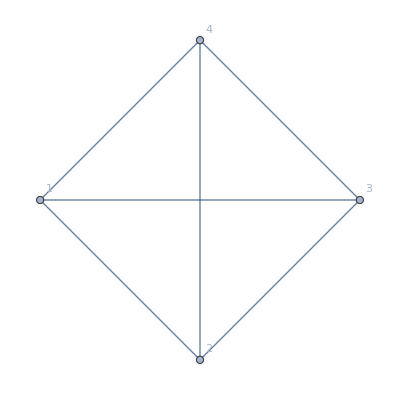
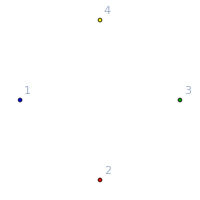
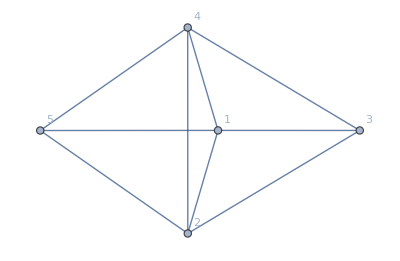
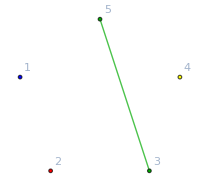
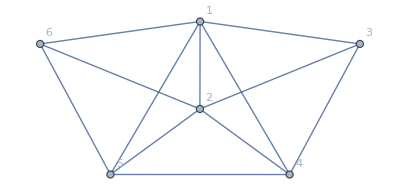
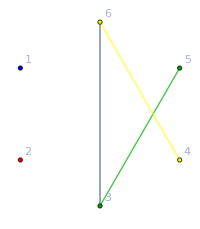
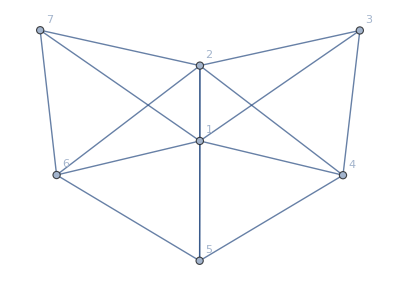
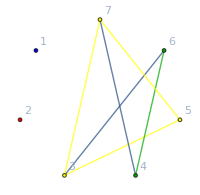
{-Graphics-→{{{{4,1}},-Graphics-}},-Graphics-→{{{{4,1},{5,1}},-Graphics-}},-Graphics-→{{{{4,1},{5,3},{6,1}},-Graphics-}},-Graphics-→{{{{4,1},{5,7},{6,6},{7,1}},-Graphics-}},-Graphics-→{{{{4,1},{5,15},{6,25},{7,10},{8,1}},-Graphics-}},-Graphics-→{{{{4,1},{5,31},{6,90},{7,65},{8,15},{9,1}},-Graphics-}},-Graphics-→{{{{4,1},{5,63},{6,301},{7,350},{8,140},{9,21},{10,1}},-Graphics-}}}

```mathematica
Table[
With[
{g=MinimalSolGraph[max]},
Graph[g,VertexLabels->"Name"]->With[{form=FindFullFormula[g,Table[{k},{k,VertexCount[g]}]]},
Table[
With[{sets=SymbolToSets[formula], colors={Blue,Red,Darker[Green],Yellow,Black}},
{SummarizeFormula[form],Graph[GraphComplement[g],
VertexStyle->Flatten[
Table[Map[#-> colors[[k]]&,sets[[k]] ],{k,Length[sets]}]
],
EdgeStyle->Flatten[
Table[Map[#[[1]]<->#[[2]]-> {Thick,colors[[k]]}&,Subsets[sets[[k]],{2}] ],{k,Length[sets]}]
],
ImageSize->200,
VertexLabels->"Name"
]
}
],
{formula,Select[form,Length[SymbolToSets[#]]==4&]}
]]],
{max,4,10}]
```

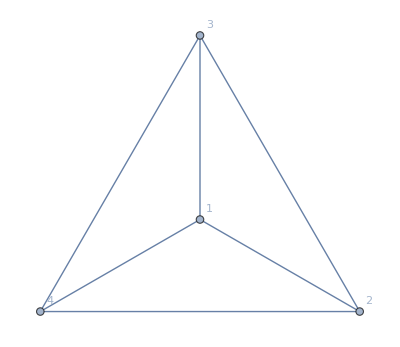
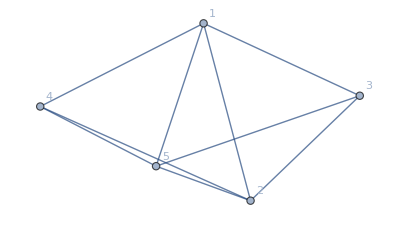
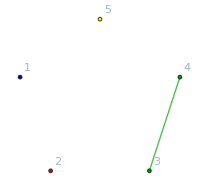
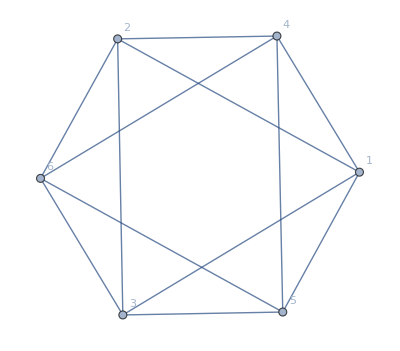
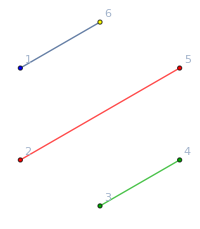
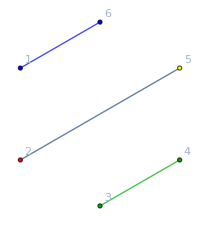
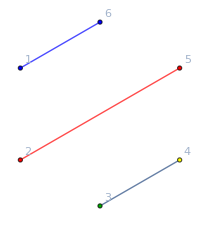
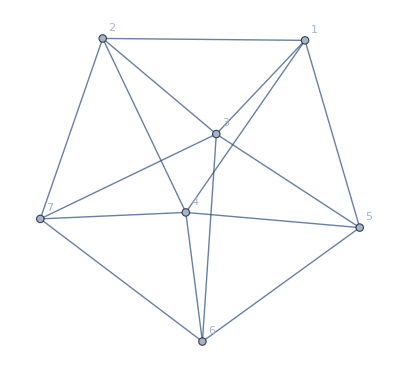
{-Graphics-→{-Graphics-},-Graphics-→{-Graphics-},-Graphics-→{-Graphics-,-Graphics-,-Graphics-},-Graphics-→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},-Graphics-→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},-Graphics-→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},-Graphics-→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[
With[
{g=JacobsThalGraph2[max]},
Graph[g,VertexLabels->"Name"]->With[{form=FindFullFormula[g,Table[{k},{k,VertexCount[g]}]]},
Table[
With[{sets=SymbolToSets[formula], colors={Blue,Red,Darker[Green],Yellow,Black}},
Graph[GraphComplement[g],
VertexStyle->Flatten[
Table[Map[#-> colors[[k]]&,sets[[k]] ],{k,Length[sets]}]
],
EdgeStyle->Flatten[
Table[Map[#[[1]]<->#[[2]]-> {Thick,colors[[k]]}&,Subsets[sets[[k]],{2}] ],{k,Length[sets]}]
],
ImageSize->200,
VertexLabels->"Name"
]
],
{formula,Select[form,Length[SymbolToSets[#]]==4&]}
]]],
{max,4,10}]
```